# Convex Optimization

```mathematica
Manipulate[Quiet@RegionPlot[{x,y}\[VectorGreaterEqual]p,{x,-2,2},{y,-2,2}],{{p,{0,0}}, Locator}]
```

```mathematica
{1,2}\[VectorLess]{3,4}
```

True

```mathematica
{1,2}\[VectorLess]{1,3}
```

False

```mathematica
{1,2}\[VectorLess]a
```

{1,2}\[VectorLess]a

```mathematica
{1,2}\[VectorLess]a/.a->3
```

True

```mathematica
{1,2}\[VectorLess]a/.a->{{1,2,3},{4,5}}
```

False

## Generalized Vector inequalities

The generalized inequality x (\[VectorGreaterEqual])_k y gives True if x-y∈ k is a proper convex cone.

Some important examples of proper cones are:

"NonNegativeCone" (ℝ_(≥0)^n)x∈ℝ^n such that x_i≥0

"NormCone" (ℚ^n)x∈ℝ^n such that Norm[{x_1,...,x_(n-1)}]≤x_n

"SemidefiniteCone" (𝕊_+^n) symmetric positive semidefinite matrices x∈ℝ^(n x n)

```mathematica
{{, {"NonNegativeCone", n}, n, x∈ℝ^n such that Subscript[x, i]>0}, {, {"NormCone", n}, n, x∈ℝ^n  such that Normpaclet:ref/Norm[{Subscript[x, 1],…,Subscript[x, n-1]}]<Subscript[x, n]}, {, "ExponentialCone", , x∈ℝ^3 such that Subscript[x, 2] ⅇ^(Subscript[x, 1]/Subscript[x, 2])<Subscript[x, 3]∧Subscript[x, 2]>0}, {, "DualExponentialCone", , x∈ℝ^3 such that -Subscript[x, 1] ⅇ^(Subscript[x, 2]/Subscript[x, 1]-1)≤Subscript[x, 3]∧Subscript[x, 1]<0}, {, {"PowerCone",α}, α, x∈ℝ^3 such that Subscript[x, 1]^α Subscript[x, 2]^(1-α)>|Subscript[x, 3]|∧Subscript[x, 1]>0 ∧Subscript[x, 2]>0}, {, {"DualPowerCone",α}, α, x∈ℝ^3 such that (Subscript[x, 1]/α)^α(Subscript[x, 2]/(1-α))^(1-α)>|Subscript[x, 3]|∧Subscript[x, 1]>0 ∧Subscript[x, 2]>0}}
```

```mathematica
{{, "NonNegativeCone", , x∈ℝ^(n×m) such that Subscript[x, i,j]>0}, {, {"SemidefiniteCone", n}, n, symmetric positive definite matrices x∈ℝ^(n×n)}}
```

```mathematica
{{, "NonNegativeCone", , x∈ℝ^(Subscript[n, 1]×⋯×Subscript[n, k]) such that Subscript[x, Subscript[i, 1],…,Subscript[i, k]]>0}}
```

#### Norm cone inequalities

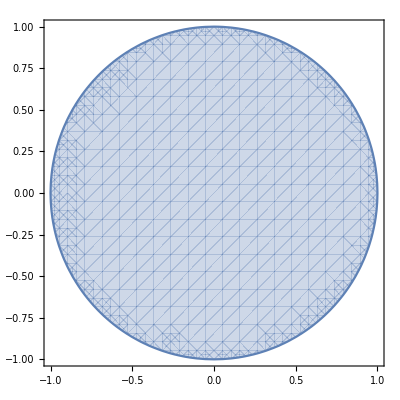

```mathematica
Quiet@RegionPlot[{x,y,1}(\[VectorGreaterEqual])_{"NormCone", 3}0,{x,-1,1},{y,-1,1}]
```

```mathematica
RegionPlot3D[{x,y,z}(\[VectorGreaterEqual])_{"NormCone", 3}0,{x,-1,1},{y,-1,1},{z,0,1}]
```

-Graphics3D-

#### Semidefinite Cone inequalities

```mathematica
{{ⅇ,1},{1,π}}(\[VectorGreaterEqual])_2 IdentityMatrix[2]
```

True

```mathematica
N[Eigenvalues[{{ⅇ,1},{1,π}}-IdentityMatrix[2]]]
```

{2.95209,0.907784}

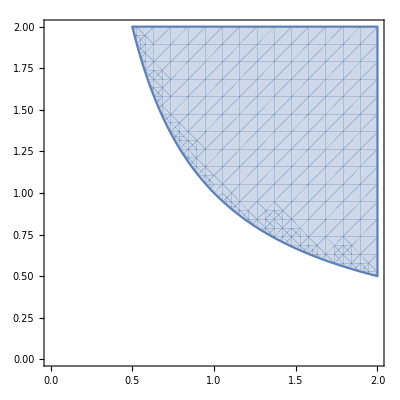

```mathematica
Quiet@RegionPlot[{{x,1},{1,y}}(\[VectorGreaterEqual])_2 0,{x,0,2},{y,0,2}]
```

```mathematica
Manipulate[Quiet@RegionPlot[{{x,1},{1,y}}(\[VectorLessEqual])_2 DiagonalMatrix[d],{x,-1,1},{y,-1,1}],{{d,{0,0}},Slider2D}]
```

## Parameter equation "Constraints"

```mathematica
parameters={a=={{1,2},{3,4},{5,6}},b=={7,8,9},λ==3};
```

```mathematica
NMinimize[{Norm[a.x-b]^2+λ Norm[x,1],parameters},x]
```

{20.7455,{x→{1.10843×10^-7,1.75893}}}

```mathematica
SetAttributes[withAssignment, HoldAll];
withAssignment[e_]:=Block[{a={{1,2},{3,4},{5,6}},b={7,8,9},λ=3},e];
```

```mathematica
withAssignment[Fit[{a,b},FitRegularization->{"L1",λ/2}]]
```

SparseArray[…]

## Model Transformation

The goal here is to transform an optimization model (a set of objective function, constraints and variable) into a form that can be used by the solvers showed above.

```mathematica
tconstraints={t\[VectorGreaterEqual]0, -t\[VectorLessEqual]x\[VectorLessEqual]t};(* Note vector inequalities *)
```

```mathematica
QuadraticOptimization[Norm[a.x-b]^2+λ Total[t], {tconstraints,parameters},{x,t}]
```

{x→{-1.78077×10^-8,1.75893},t→{1.84981×10^-8,1.75893}}

## Convexity

A set C is affine if for x, y in C then θ x + (1-θ)y is also in C

A set C is convex if the above holds with θ >= 0

A function f is convex if f(θ x + (1-θ)y) <= θ f(x)+(1-θ)f(y) for θ>=0 and all x, y in the domain of f.

The epigraph of  a function is the set {x, t} such that x is in the domain of f and f(x) <= t

```mathematica
f[x_]:=x^2
constrain[{x_,_}]:={x, f[x]};
plot=Plot[f[x],{x,-1,1},Filling->Top];
DynamicModule[{px={-1,1}, py={1,1}},
Show[plot, Graphics[{Dynamic[Line[{px,py}]],
Locator[Dynamic[px, Function[px=constrain[#]]]],
Locator[Dynamic[py, Function[py=constrain[#]]]]}]]]
```

## Convex Optimization

A convex optimization problem is to

minimize f(x)
subject to g(x) <= 0 and h(x) ==0

where f and g = {g_1,....} are convex functions and h is affine

So any convex optimization problem may be expressed as optimization of a linear function over a convex set.

This is a convex problem

```mathematica
FindMinimum[{x.{3,4},x\[VectorGreaterEqual]0,x∈Disk[]},x]
```

{-7.59942×10^-7,{x→{-9.1193×10^-8,-1.21591×10^-7}}}

This is not a convex problem

```mathematica
FindMinimum[{x.{3,4},x\[VectorGreaterEqual]0,x∈Circle[]},x]
```

{3.,{x→{1.,1.27271×10^-8}}}

## Conic Optimization

A convex optimization problem is to minimize c.x
subject to h(x)==0 and g_j(x)≤0 for j=1,...k

Yet another way of expressing it is to minimize c.x
subject to a_o.x+b_o==0 and a_j.x+b_j(\[VectorGreaterEqual])_k_j 0
where k_j is a convex proper cone j=1,...,k

This is called a conic linear optimization problem.

## Model Transformation Revisited

The general goal for the convex model transformation is to reduce a given optimization problem into a conic linear optimization problem.

An alternative to transforming the fitting problem (minimize Norm[a.x-n]^2 +λ Norm[x,1]) to quadratic optimization form is to get the linear conic form. Since both Norm[a.x-b] and Norm[x,1] are convex, the problem can be expressed as

minimize s + λ t
subject to u^2≤t, Norm[a.x+b]<=u and Norm[x,1]<=t

```mathematica
ConicOptimization[s+λ t, {u^2≤s, Norm[a.x-b]≤u,Norm[x,1]≤t,parameters},{x,s,t,u}]
```

{x→{1.57723×10^-7,1.75893},s→15.4688,t→1.75893,u→3.93304}